# Backbending in nuclei

```mathematica
energies158=Sort[{6026.8,5327.4,4679.5,4026.1,3374.29,2680.79,2072.53,1493.47,970.34,527.22,192.15,0.0}];
energies1582=Sort[{4948.9,4272.4,3668.2,3109.3,2488.0,2019.1,1589.5,1257.28,989.08,806.38}];
spins158=Table[i,{i,0,22,2}];
spins1582=Table[i,{i,0,18,2}];
```

## MOIS and Rotational Frequencies

```mathematica
mois[energies_,spins_]:=Table[(4*spins[[i]]-2)/((energies[[i]]-energies[[i-1]])/1000),{i,2,Length[energies]}];
hrots[energies_,spins_]:=Table[Sqrt[4*(spins[[i]]^2-spins[[i]]+1)*(((energies[[i]]-energies[[i-1]])/1000)/(4*spins[[i]]-2))^2],{i,2,Length[energies]}];
hrotsSquared[energies_,spins_]:=#^2&/@hrots[energies,spins];
```

## Plots

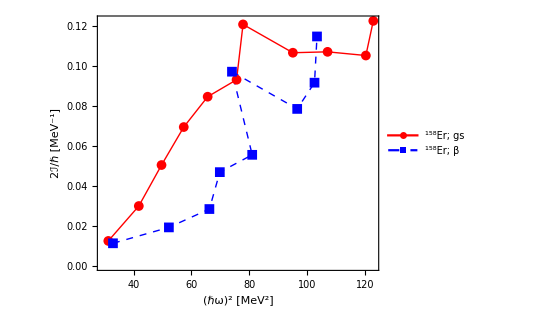

```mathematica
Er158Data=Table[{mois[energies158,spins158][[i]],hrotsSquared[energies158,spins158][[i]]},{i,1,Length[mois[energies158,spins158]]}];
Er158Data2=Table[{mois[energies1582,spins1582][[i]],hrotsSquared[energies1582,spins1582][[i]]},{i,1,Length[hrotsSquared[energies1582,spins1582]]}];
ListPlot[{Er158Data,Er158Data2},Joined->True,Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[{nucleus["Er; gs","158"],nucleus["Er; β","158"]},Scaled[{0.76,0.3}]],LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"(ℏω)^2 [MeV^2]","2ℐ/ℏ [MeV^-1]"},ImageSize->400]
```